## Model with idiosyncratic noise

```mathematica
β=.; (* confirmation bias *)
p=.; (* group coupling *)
θ=.; (* idiosyncratic noise *)
ρ=.; (* state-dependent noise *)

M = 4;
f[oi_,oj_,β_,θ_]:=(1-θ)(-oi+oj+(1-oi oj) Tanh[(oi β)/2])/(4 M)-θ oi
p = 1/2;
oAchange[oA_,oB_,β_,θ_]:= (1-p)f[oA,oA,β,θ]+ p f[oA,oB,β,θ]
oBchange[oA_,oB_,β_,θ_]:= (1-p)f[oB,oB,β,θ]+ p f[oB,oA,β,θ]
```

```mathematica
θ=1/100;
NSolveValues[{oAchange[oA,oB,4,θ] == 0&&oBchange[oA,oB,4,θ]==0&&oA>=-1&&oA<=1&&oB>=-1&&oB<=1},{oA,oB},Reals]
```

{{-0.918593,-0.918593},{-0.849436,0.348817},{-0.791089,0.791089},{-0.348817,0.849436},{0,0},{0.348817,-0.849436},{0.791089,-0.791089},{0.849436,-0.348817},{0.918593,0.918593}}

## noise bifurcation

```mathematica
samples=50;
θmax = 1/10;
θ = .;
β = 6;

sols = Table[NSolveValues[{oAchange[oA,oB,β,θmax sample/samples] == 0&&oBchange[oA,oB,β,θmax sample/samples]==0&&oA>=-1&&oA<=1&&oB>=-1&&oB<=1},{oA,oB},Reals],{sample,1,samples,1}
];
```

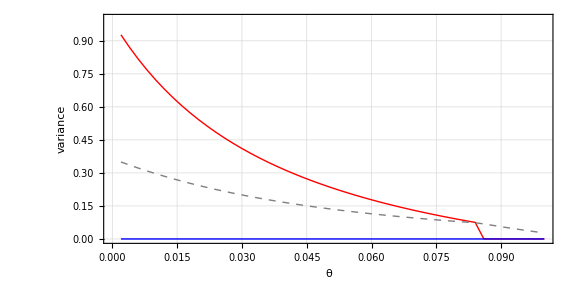

```mathematica
pdθ =  Table[PadRight[1/2 Variance[Transpose[sols[[sample,;;,;;]]]],9],{sample,1,samples,1}];
gmfθ = ListPlot[Transpose[pdθ[[;;,{3,1,2}]]],Joined->True,ImageSize->Large,DataRange->{θmax /samples,θmax},Frame->True,PlotRange->{Automatic,{0,1}},GridLines->Automatic,AspectRatio->1/2,PlotStyle->{{Red,Thick},{Blue,Thick},{Gray,Dashed,Thick}},(*PlotMarkers->{Graphics[{Disk[]}],8},*)Frame->True,FrameLabel->{"θ","variance"},BaseStyle->{Large,FontFamily->"Helvetica"},ImageSize->800,GridLines->Automatic]
```

## β bifurcation

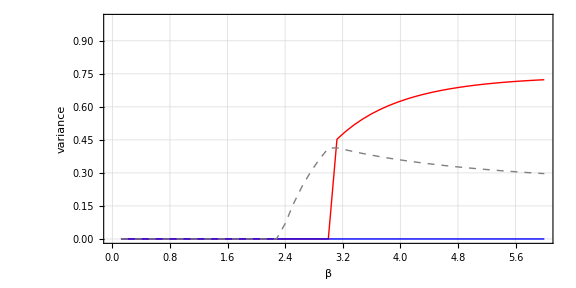

```mathematica
samples=50;
θ = 0;
θ = 1/100;
βmax = 6;

sols = Table[NSolveValues[{oAchange[oA,oB,βmax sample/samples,θ] == 0&&oBchange[oA,oB,βmax sample/samples,θ]==0&&oA>=-1&&oA<=1&&oB>=-1&&oB<=1},{oA,oB},Reals],{sample,1,samples,1}
];
pdβ =  Table[PadRight[1/2 Variance[Transpose[sols[[sample,;;,;;]]]],9],{sample,1,samples,1}];
gmfβ = ListPlot[Transpose[pdβ[[;;,{3,1,2}]]],Joined->True,ImageSize->Large,DataRange->{βmax /samples,βmax},Frame->True,PlotRange->{Automatic,{0,1}},GridLines->Automatic,AspectRatio->1/2,PlotStyle->{{Red,Thick},{Blue,Thick},{Gray,Dashed,Thick}},(*PlotMarkers->{Graphics[{Disk[]}],8},*)Frame->True,FrameLabel->{"β","variance"},BaseStyle->{Large,FontFamily->"Helvetica"},ImageSize->800,GridLines->Automatic]
```

## Model with argument and idiosyncratic noise

```mathematica
β=.; (* confirmation bias *)
p=.; (* group coupling *)
θ=.; (* idiosyncratic noise *)
ρ=.; (* state-dependent noise *)

M = 4;
f[oi_,oj_,β_,θ_]:=(1-θ)(-oi+oj+(1-oi oj) Tanh[(oi β)/2])/(4 M)-θ oi

oAchange[oA_,oB_,β_,p_,θ_,ρ_]:= (1-ρ)( (1-p)f[oA,oA,β,θ]+ p f[oA,oB,β,θ] )  + ρ f[oA,0,β,θ]
oBchange[oA_,oB_,β_,p_,θ_,ρ_]:= (1-ρ)( (1-p)f[oB,oB,β,θ]+ p f[oB,oA,β,θ] ) + ρ f[oB,0,β,θ]

(*oAchange[oA_,oB_,β_,p_,θ_]:= ( (1-p)f[oA,oA,β,θ]+ p f[oA,oB,β,θ] )  
oBchange[oA_,oB_,β_,p_,θ_]:= ( (1-p)f[oB,oB,β,θ]+ p f[oB,oA,β,θ] ) *)
```

```mathematica
M = .;
FullSimplify[oAchange[oA,oB,β,p,θ,ρ]]
FullSimplify[oBchange[oA,oB,β,p,θ,ρ]]
```

1/(4 M)(oB p (-1+θ) (-1+ρ)-oA (4 M θ+p (-1+θ) (-1+ρ)+ρ-θ ρ)+(-1+θ) (-1+oA (oA (-1+p)-oB p) (-1+ρ)) Tanh[(oA β)/2])

1/(4 M)(oA p (-1+θ) (-1+ρ)-oB (4 M θ+p (-1+θ) (-1+ρ)+ρ-θ ρ)+(-1+θ) (-1+oB (oB (-1+p)-oA p) (-1+ρ)) Tanh[(oB β)/2])

```mathematica
θ=0;
ρ=1;
β = 4;
p = 1/2;
NSolveValues[{oAchange[oA,oB,β,p,θ,ρ] == 0&&oBchange[oA,oB,β,p,θ,ρ]==0&&oA>=-1&&oA<=1&&oB>=-1&&oB<=1},{oA,oB},Reals]
```

{{-0.957504,-0.957504},{0.,-0.957504},{0.957504,-0.957504},{-0.957504,0.},{0.,0.},{0.957504,0.},{-0.957504,0.957504},{0.,0.957504},{0.957504,0.957504}}

## noise bifurcation

```mathematica
samples=50;
ρmax = 1/1;
θ = 0;
β = 5/2;
p=1/2;
M = 4;

sols = Table[NSolveValues[{oAchange[oA,oB,β,p,θ,ρmax sample/samples] == 0&&oBchange[oA,oB,β,p,θ,ρmax sample/samples]==0&&oA>=-1&&oA<=1&&oB>=-1&&oB<=1},{oA,oB},Reals],{sample,1,samples,1}
];
```

{50}

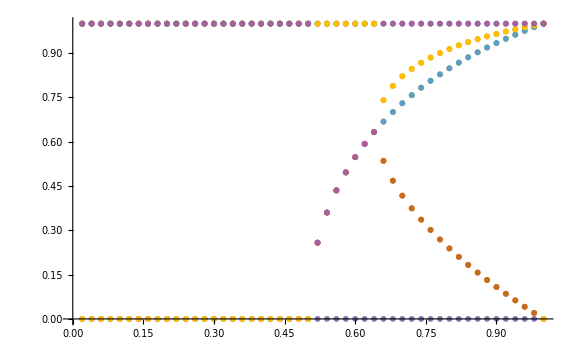

```mathematica
Dimensions[sols]
solsP3 = Table[CenterArray[sols[[sample]], 9,sols[[sample]]],{sample,1,samples,1}];
ListPlot[Transpose[Abs[solsP3[[;;,;;,1]]]],Joined->False,ImageSize->Automatic,DataRange->{ρmax /samples,ρmax}]
```

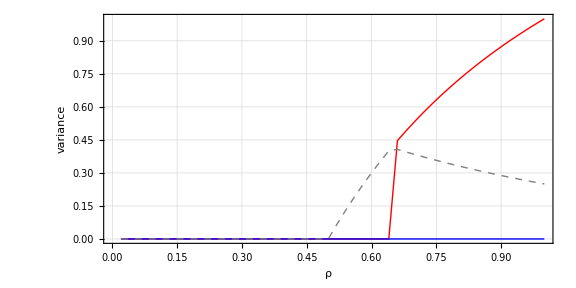

```mathematica
pdρ =  Table[PadRight[1/2 Variance[Transpose[sols[[sample,;;,;;]]]],9],{sample,1,samples,1}];
gmfρ = ListPlot[Transpose[pdρ[[;;,{3,1,2}]]],Joined->True,ImageSize->Large,DataRange->{ρmax /samples,ρmax},Frame->True,PlotRange->{Automatic,{0,1}},GridLines->Automatic,AspectRatio->1/2,PlotStyle->{{Red,Thick},{Blue,Thick},{Gray,Dashed,Thick}},(*PlotMarkers->{Graphics[{Disk[]}],8},*)Frame->True,FrameLabel->{"ρ","variance"},BaseStyle->{Large,FontFamily->"Helvetica"},ImageSize->800,GridLines->Automatic]
```

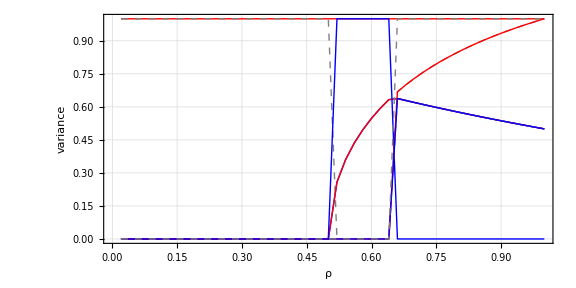

```mathematica
pdρe =  Table[PadRight[ Mean[Transpose[Abs[sols[[sample,;;,;;]]]]],9],{sample,1,samples,1}];
gmfρe = ListPlot[Transpose[pdρe[[;;,;;]]],Joined->True,ImageSize->Large,DataRange->{ρmax /samples,ρmax},Frame->True,PlotRange->{Automatic,{0,1}},GridLines->Automatic,AspectRatio->1/2,PlotStyle->{{Red,Thick},{Blue,Thick},{Gray,Dashed,Thick}},(*PlotMarkers->{Graphics[{Disk[]}],8},*)Frame->True,FrameLabel->{"ρ","variance"},BaseStyle->{Large,FontFamily->"Helvetica"},ImageSize->800,GridLines->Automatic]
```

## network bifurcation

```mathematica
samples=50;
pmax = 1/2;
θ = 0;
β = 1;
ρ=0;

sols = Table[NSolveValues[{oAchange[oA,oB,β,pmax-pmax sample/samples,θ,ρ] == 0&&oBchange[oA,oB,β,pmax-pmax sample/samples,θ,ρ]==0&&oA>=-1&&oA<=1&&oB>=-1&&oB<=1},{oA,oB},Reals],{sample,1,samples,1}
];
```

{50}

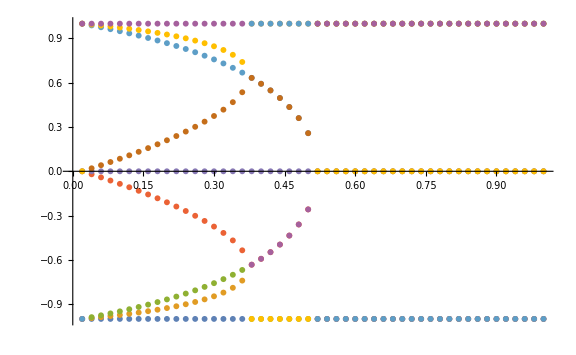

```mathematica
Dimensions[sols]
solsP3 = Table[CenterArray[sols[[sample]], 9,sols[[sample]]],{sample,1,samples,1}];
ListPlot[Transpose[solsP3[[;;,;;,1]]],Joined->False,ImageSize->Automatic,DataRange->{ρmax ,ρmax/samples}]
```

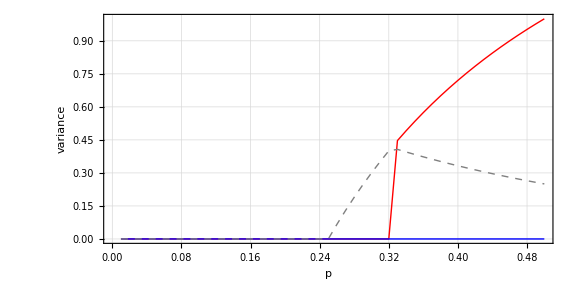

```mathematica
pdp =  Table[PadRight[1/2 Variance[Transpose[sols[[sample,;;,;;]]]],9],{sample,1,samples,1}];
gmfp = ListPlot[Transpose[pdp[[;;,{3,1,2}]]],Joined->True,ImageSize->Large,DataRange->{pmax /samples,pmax},Frame->True,PlotRange->{Automatic,{0,1}},GridLines->Automatic,AspectRatio->1/2,PlotStyle->{{Red,Thick},{Blue,Thick},{Gray,Dashed,Thick}},(*PlotMarkers->{Graphics[{Disk[]}],8},*)Frame->True,FrameLabel->{"p","variance"},BaseStyle->{Large,FontFamily->"Helvetica"},ImageSize->800,GridLines->Automatic]
```